## Imtek`Sudoku`

This package solves the sudoku game. Given a game specification as an array, solutions can be generated and plotted. The package uses the exhausive search exact cover algorithm of Donald Knuth to find all possible solutions of the puzzle.

ReadSudoku[ file ] | reads a sudoku specification from an ASCII file and returns it as a 9×9 integer-valued matrix. The specification has a character entry for each matrix entry of the puzzle. Empty sites are specified by the zero, blank and fullstop characters, all other entries are digits. In the returned matrix, empty sites are marked by zero entries. 
DrawSudoku[ matrix ] | draws a picture of the sudoku puzzle specified by the integer-valued matrix..
SolveSudoku[ matrix ] | solves the sudoku puzzle specified by the integer-valued matrix. A list of zero or more matrix solutions are returned.

Sudoku functions.

First we import the package:

```mathematica
Needs["Sudoku`"]
```

```mathematica
<<(NotebookDirectory[]<>"Sudoku.m")
```

First we read a problem specification from file:

```mathematica
puzzle=ReadSudoku[NotebookDirectory[]<>"puzzle2"]
```

{{0,0,0,3,0,0,8,0,0},{6,4,0,8,0,0,0,5,0},{8,7,5,0,0,0,0,0,1},{5,0,0,0,7,0,2,0,6},{0,0,0,0,9,0,0,0,0},{2,0,9,0,8,0,0,0,5},{4,0,0,0,0,0,7,6,9},{0,2,0,0,0,8,0,1,3},{0,0,7,0,0,5,0,0,0}}

We can plot the layout of the puzzle:

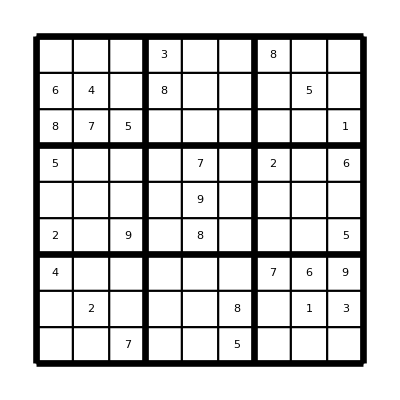

```mathematica
Show[DrawSudoku[puzzle]]
```

We now solve the puzzle (there may be more than one solution!):

```mathematica
sol=SolveSudoku[puzzle]
```

{{{1,9,2,3,5,6,8,4,7},{6,4,3,8,1,7,9,5,2},{8,7,5,4,2,9,6,3,1},{5,8,4,1,7,3,2,9,6},{7,6,1,5,9,2,3,8,4},{2,3,9,6,8,4,1,7,5},{4,5,8,2,3,1,7,6,9},{9,2,6,7,4,8,5,1,3},{3,1,7,9,6,5,4,2,8}}}

Since we get a list of solutions, we map the plotting function to the solution object:

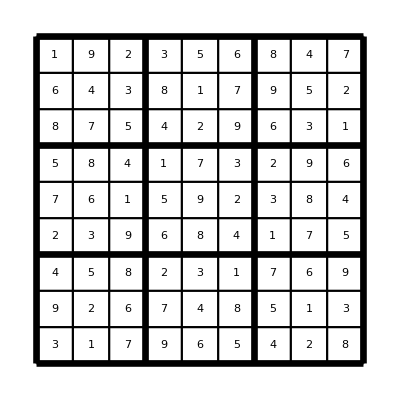

```mathematica
Show[(DrawSudoku[#1]&)/@sol]
```